```mathematica
CurrentValue[EvaluationNotebook[],DefaultNaturalLanguage]="Spanish";
```

```mathematica
(mat={{1,2,3},{4,5,6},{7,8,9}})//MatrixForm
```

(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9)

```mathematica
Minors[{{1,2,3},{4,5,6},{7,8,9}},2,Identity]//MatrixForm
```

((1 | 2
4 | 5) | (1 | 3
4 | 6) | (2 | 3
5 | 6)
(1 | 2
7 | 8) | (1 | 3
7 | 9) | (2 | 3
8 | 9)
(4 | 5
7 | 8) | (4 | 6
7 | 9) | (5 | 6
8 | 9))

```mathematica
(mat=Array[Subscript[a,##]&,{3,3}])//MatrixForm
```

(a_(1,1) | a_(1,2) | a_(1,3)
a_(2,1) | a_(2,2) | a_(2,3)
a_(3,1) | a_(3,2) | a_(3,3))

```mathematica
Diagonal[Map[Reverse,Minors[mat,#],{0,1}]]&/@{1,2,3}
```

{{a_(3,3),a_(2,2),a_(1,1)},{-a_(2,3) a_(3,2)+a_(2,2) a_(3,3),-a_(1,3) a_(3,1)+a_(1,1) a_(3,3),-a_(1,2) a_(2,1)+a_(1,1) a_(2,2)},{-a_(1,3) a_(2,2) a_(3,1)+a_(1,2) a_(2,3) a_(3,1)+a_(1,3) a_(2,1) a_(3,2)-a_(1,1) a_(2,3) a_(3,2)-a_(1,2) a_(2,1) a_(3,3)+a_(1,1) a_(2,2) a_(3,3)}}

```mathematica
Minors[mat,#]&/@{1,2,3}
```

{{{a_(1,1),a_(1,2),a_(1,3)},{a_(2,1),a_(2,2),a_(2,3)},{a_(3,1),a_(3,2),a_(3,3)}},{{-a_(1,2) a_(2,1)+a_(1,1) a_(2,2),-a_(1,3) a_(2,1)+a_(1,1) a_(2,3),-a_(1,3) a_(2,2)+a_(1,2) a_(2,3)},{-a_(1,2) a_(3,1)+a_(1,1) a_(3,2),-a_(1,3) a_(3,1)+a_(1,1) a_(3,3),-a_(1,3) a_(3,2)+a_(1,2) a_(3,3)},{-a_(2,2) a_(3,1)+a_(2,1) a_(3,2),-a_(2,3) a_(3,1)+a_(2,1) a_(3,3),-a_(2,3) a_(3,2)+a_(2,2) a_(3,3)}},{{-a_(1,3) a_(2,2) a_(3,1)+a_(1,2) a_(2,3) a_(3,1)+a_(1,3) a_(2,1) a_(3,2)-a_(1,1) a_(2,3) a_(3,2)-a_(1,2) a_(2,1) a_(3,3)+a_(1,1) a_(2,2) a_(3,3)}}}

```mathematica
MatrixForm/@Map[Reverse,Minors[mat,#],{0,1}]&/@{1,2,3}
```

{{(a_(3,3)
a_(3,2)
a_(3,1)),(a_(2,3)
a_(2,2)
a_(2,1)),(a_(1,3)
a_(1,2)
a_(1,1))},{(-a_(2,3) a_(3,2)+a_(2,2) a_(3,3)
-a_(2,3) a_(3,1)+a_(2,1) a_(3,3)
-a_(2,2) a_(3,1)+a_(2,1) a_(3,2)),(-a_(1,3) a_(3,2)+a_(1,2) a_(3,3)
-a_(1,3) a_(3,1)+a_(1,1) a_(3,3)
-a_(1,2) a_(3,1)+a_(1,1) a_(3,2)),(-a_(1,3) a_(2,2)+a_(1,2) a_(2,3)
-a_(1,3) a_(2,1)+a_(1,1) a_(2,3)
-a_(1,2) a_(2,1)+a_(1,1) a_(2,2))},{(-a_(1,3) a_(2,2) a_(3,1)+a_(1,2) a_(2,3) a_(3,1)+a_(1,3) a_(2,1) a_(3,2)-a_(1,1) a_(2,3) a_(3,2)-a_(1,2) a_(2,1) a_(3,3)+a_(1,1) a_(2,2) a_(3,3))}}

```mathematica
(Map[Reverse,Minors[mat,#],{0,1}]//Diagonal)&/@{1,2,3}
```

{{a_(3,3),a_(2,2),a_(1,1)},{-a_(2,3) a_(3,2)+a_(2,2) a_(3,3),-a_(1,3) a_(3,1)+a_(1,1) a_(3,3),-a_(1,2) a_(2,1)+a_(1,1) a_(2,2)},{-a_(1,3) a_(2,2) a_(3,1)+a_(1,2) a_(2,3) a_(3,1)+a_(1,3) a_(2,1) a_(3,2)-a_(1,1) a_(2,3) a_(3,2)-a_(1,2) a_(2,1) a_(3,3)+a_(1,1) a_(2,2) a_(3,3)}}

```mathematica
(mat=QC[{1,0,0,1},1]//Reshuffle)//MatrixForm
```

(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1)

```mathematica
Diagonal[Map[Reverse,Minors[mat,#],{0,1}]]&/@{1,2,3,4}
```

{{1,0,0,1},{0,0,0,1,0,0},{0,0,0,0},{0}}

### Submatriz principal

Consideremos una matriz A de dimensión n×n. Sea n^- el conjunto {1,2,3,… ,n}, es decir el conjunto con los índices de las entradas de A. Por otro lado, J⊂n^-. Una submatriz principal A_J es la submatriz de A que se obtiene de borrar la k-ésima fila y columna de A, para todo k que pertenece al conjunto n^--J. 

Por ejemplo, si 
                                                                                                     A=(a | b | c
d | e | f
g | h | i),
entonces 
                                                                    A_{2}=(e)        y       A_{1,3}=(a | c
g | i).

### Menores principales

Un menor principal es el determinante de una submatriz principal.

### Positividad semidefinida de matrices Hermíticas

Una condición necesaria y suficiente para que una matriz Hermítica sea positiva semidefinida es que todos los menores principales de la matriz sean no negativos. 

Veamos un ejemplo con nuestros canales:

```mathematica
(choi=QC[{1,0,1,0},1]//Reshuffle)//MatrixForm
```

(1/2 | 0 | 0 | 1/2
0 | 1/2 | -1/2 | 0
0 | -1/2 | 1/2 | 0
1/2 | 0 | 0 | 1/2)

```mathematica
Ptest[choi]
```

True

```mathematica
QC[KroneckerProduct[{1,1,0,0},{1,1,1,1}]//Flatten,2]//Reshuffle//Ptest
```

$Aborted

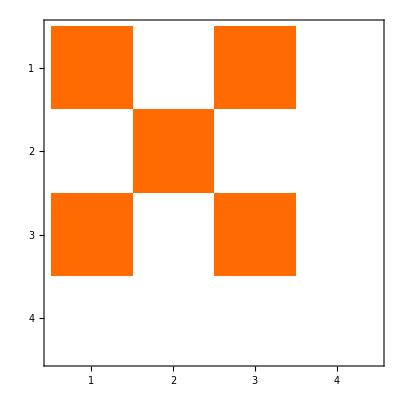

```mathematica
Normal[SparseArray[{{1,1},{1,3},{3,1},{3,3},{2,2}}->ConstantArray[1,{5}],{4,4}]]//MatrixPlot
```

```mathematica
(mat=SparseArray[{{1,1}->1,{1,3}->1,{3,1}->1,{3,3}->1,{2,2}->a,{2,4}->a,{4,2}->a,{4,4}->a,{4,3}->b},{4,4}]//Normal)//MatrixForm
```

(1 | 0 | 1 | 0
0 | a | 0 | a
1 | 0 | 1 | 0
0 | a | b | a)

```mathematica
$Assumptions=(a==1∨a==0);
And@@(#≥0&/@(QC[mat//Flatten,2]//Reshuffle//Eigenvalues))//FullSimplify
```

b==0

```mathematica
(simplerState=SparseArray[{{1,1}->1,{1,3}->1,{3,1}->1,{3,3}->1,{3,2}->1,{4,4}->1},{4,4}]//Normal)//MatrixForm
Pauli[#]&/@(Position[simplerState,1]-1)//Total//MatrixForm
```

(1 | 0 | 1 | 0
0 | 0 | 0 | 0
1 | 1 | 1 | 0
0 | 0 | 0 | 1)

(2 | -ⅈ | -ⅈ | -1-ⅈ
ⅈ | 0 | 1-ⅈ | -ⅈ
ⅈ | 1+ⅈ | 0 | -ⅈ
-1+ⅈ | ⅈ | ⅈ | 2)

```mathematica
Bell0=1/2KroneckerProduct[{1,0,0,0}+{0,0,0,1},{1,0,0,0}+{0,0,0,1}];
Bell1=1/2KroneckerProduct[{1,0,0,0}-{0,0,0,1},{1,0,0,0}-{0,0,0,1}];
Bell2=1/2KroneckerProduct[{0,1,0,0}+{0,0,1,0},{0,1,0,0}+{0,0,1,0}];
Bell3=1/2KroneckerProduct[{0,1,0,0}-{0,0,1,0},{0,1,0,0}-{0,0,1,0}];
Bell4=1/2KroneckerProduct[{1,0,0,0}+{0,0,0,1},{1,0,0,0}-{0,0,0,1}];
Bell5=1/2KroneckerProduct[{0,1,0,0}+{0,0,1,0},{1,0,0,0}+{0,0,0,1}];
Bell6=1/2KroneckerProduct[{0,1,0,0}+{0,0,1,0},{1,0,0,0}-{0,0,0,1}];
Bell7=1/2KroneckerProduct[{1,0,0,0}-{0,0,0,1},{0,1,0,0}+{0,0,1,0}];
```

```mathematica
Bell3//MatrixForm
```

(0 | 0 | 0 | 0
0 | 1/2 | -1/2 | 0
0 | -1/2 | 1/2 | 0
0 | 0 | 0 | 0)

```mathematica
Bell0+Bell1//MatrixForm
```

(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1)

```mathematica
(simplerState=ArrayReshape[Inverse[ChangeOfBasisMatrix[2]].(1/2Bell0+1/2Bell1//Flatten),{4,4}])//MatrixForm
```

(1/4 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1/4)

```mathematica
1/4Pauli[{0,0}]+1/4Pauli[{3,3}]//MatrixForm
```

(1/2 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1/2)

```mathematica
Pauli[#]&/@{{0,0},{0,2},{2,0},{2,2}}//Total//MatrixForm
```

(1 | -ⅈ | -ⅈ | -1
ⅈ | 1 | 1 | -ⅈ
ⅈ | 1 | 1 | -ⅈ
-1 | ⅈ | ⅈ | 1)

```mathematica
(Pauli[#]&/@{{0,0},{0,2},{2,0},{2,2}}//Total)+1/2Pauli[{0,0}]+1/2Pauli[{3,3}]//MatrixForm
```

(2 | -ⅈ | -ⅈ | -1
ⅈ | 1 | 1 | -ⅈ
ⅈ | 1 | 1 | -ⅈ
-1 | ⅈ | ⅈ | 2)

```mathematica
Bell3//MatrixForm
```

(0 | 0 | 0 | 0
0 | 1/2 | -1/2 | 0
0 | -1/2 | 1/2 | 0
0 | 0 | 0 | 0)